```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\VS_workspace\CPlusPlus\SOHR\projects\catalytic_cycle\theory\SSA

## S⇌_(k_-S)^k_S(A⇌_(k_-1)^k_1 B)⟶^k_B P

### Solve differential equation like (eq 1)d[S]/dt=-k_S[S]+k_-S[A] (eq 2)d[A]/dt=k_S[S]+k_-1[B]-(k_1+k_-S)[A] (eq 3)d[B]/dt=k_1[A]-(k_B+k_-1)[B]

```mathematica
eq1=-Subscript[k, S]*xS+Subscript[k, -S]*xA;
eq2=Subscript[k, S]*xS+Subscript[k, -1]*xB-(Subscript[k, 1]+Subscript[k, -S])*xA;
eq3=Subscript[k, 1]*xA-(Subscript[k, B]+Subscript[k, -1])*xB;
eq4=Subscript[k, B]*xB;
eqz=xZ-(xA+xB);
```

#### Make a Steady State Approximation (SSA), let (eq 2) = 0 and (eq 3) = 0

```mathematica
Clear[soln];soln=Solve[eq2==0&&eq3==0&&eqz==0,{xS,xA,xB}]//Simplify
```

{{xS→(xZ (k_1 k_B+(k_-1+k_B) k_-S))/((k_-1+k_1+k_B) k_S),xA→(xZ (k_-1+k_B))/(k_-1+k_1+k_B),xB→(xZ k_1)/(k_-1+k_1+k_B)}}

```mathematica
xA=xA/.soln[[1,2]];xB=xB/.soln[[1,3]];
```

#### Rate Constant of Z

```mathematica
Subscript[k, Z]=(Subscript[k, -S]*xA+Subscript[k, B]*xB)/xZ//Simplify
```

(k_1 k_B+(k_-1+k_B) k_-S)/(k_-1+k_1+k_B)

#### Branching Ratios

```mathematica
Subscript[Γ, S]=Numerator[xA]*Subscript[k, -S]/xZ//Simplify
```

(k_-1+k_B) k_-S

```mathematica
Subscript[Γ, P]=Numerator[xB]*Subscript[k, B]/xZ//Simplify
```

k_1 k_B

```mathematica
bs=Subscript[Γ, S]/(Subscript[Γ, S]+Subscript[Γ, P])
```

((k_-1+k_B) k_-S)/(k_1 k_B+(k_-1+k_B) k_-S)

```mathematica
bp=Subscript[Γ, P]/(Subscript[Γ, S]+Subscript[Γ, P])
```

(k_1 k_B)/(k_1 k_B+(k_-1+k_B) k_-S)

```mathematica
Clear[xA,xB,xS,xC,xZ,xP];
LHS={D[xS[t],t],D[xA[t],t],D[xB[t],t],D[xP[t],t]};
RHS={eq1,eq2,eq3,eq4}/.{Subscript[k, S]->k1,Subscript[k, -S]->k2,Subscript[k, 1]->k3,Subscript[k, -1]->k4,Subscript[k, B]->k5,xS->xS[t],xA->xA[t],xB->xB[t],xP->xP[t]};
deqs={LHS⟦1⟧==RHS⟦1⟧,LHS⟦2⟧==RHS⟦2⟧,LHS⟦3⟧==RHS⟦3⟧,LHS⟦4⟧==RHS⟦4⟧,xS[0]==0,xA[0]==1,xB[0]==0,xP[0]==0}
vars={xS[t],xA[t],xB[t],xP[t]}
```

{xS'[t]==k2 xA[t]-k1 xS[t],xA'[t]==-(k2+k3) xA[t]+k4 xB[t]+k1 xS[t],xB'[t]==k3 xA[t]-(k4+k5) xB[t],xP'[t]==k5 xB[t],xS[0]==0,xA[0]==1,xB[0]==0,xP[0]==0}

{xS[t],xA[t],xB[t],xP[t]}

```mathematica
(*Here we calculate the concentration of P*)
Clear[ExactSolnP];ExactSolnP[k1_,k2_,k3_,k4_,k5_,t_,tmin_,tmax_]:=
Module[{soln,output,xS,xA,xB,xP},
soln=NDSolve[{xS'[t]==k2 xA[t]-k1 xS[t],xA'[t]==-(k2+k3) xA[t]+k4 xB[t]+k1 xS[t],xB'[t]==k3 xA[t]-(k4+k5) xB[t],xP'[t]==k5 xB[t],xS[0]==0,xA[0]==1,xB[0]==0,xP[0]==0},{xS[t],xA[t],xB[t],xP[t]},{t,tmin,tmax} ];
output[t]=Simplify[xP[t]/.Last[soln],Assumptions->{k1>0,k2>0,k3>0,k4>0,k5>0,t>0}];
Return[output];]
```

(k3 k5+k2 (k4+k5))/(k3+k4+k5)

(k3 k5)/(k3 k5+k2 (k4+k5))

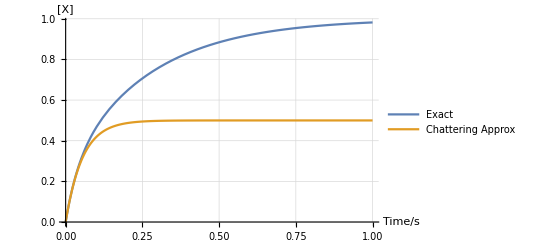

```mathematica
keff=Subscript[k, Z]/.{Subscript[k, S]->k1,Subscript[k, -S]->k2,Subscript[k, 1]->k3,Subscript[k, -1]->k4,Subscript[k, B]->k5};
keff
bpeff=bp/.{Subscript[k, S]->k1,Subscript[k, -S]->k2,Subscript[k, 1]->k3,Subscript[k, -1]->k4,Subscript[k, B]->k5};
bpeff
Value0={10^13,10^13,10^16,10^17,10^14};
tend=10^-12;
Value1={k1->Value0⟦1⟧,k2->Value0⟦2⟧,k3->Value0⟦3⟧,k4->Value0⟦4⟧,k5->Value0⟦5⟧};
fplot=ExactSolnP[Value0⟦1⟧,Value0⟦2⟧,Value0⟦3⟧,Value0⟦4⟧,Value0⟦5⟧,t,0,tend];
Plot[{Evaluate[fplot[t]],(1-ⅇ^(-(keff)*t))*bpeff/.Value1},{t,0,tend},PlotRange->All,PlotLegends->{"Exact","Chattering Approx"},GridLines->Automatic,AxesLabel->{"Time/s","[X]"}]
```